```mathematica
KsetPartitionsWithPattern[nodes_,pattern_]:=Select[KSetPartitions[Range[nodes],4],PartitionHasPatternFast[#,pattern]&]
```

```mathematica
quad1[nodes_]:=KsetPartitionsWithPattern[nodes,{{1},{2},{3,5},{4}}]
```

```mathematica
quad2[nodes_]:=KsetPartitionsWithPattern[nodes,{{1,3},{2},{4},{5}}]
```

```mathematica
quad3[nodes_]:=KsetPartitionsWithPattern[nodes,{{1,4},{2},{3},{5}}]
```

```mathematica
quad4[nodes_]:=KsetPartitionsWithPattern[nodes,{{1},{2,5},{3},{4}}]
```

```mathematica
quad5[nodes_]:=KsetPartitionsWithPattern[nodes,{{1},{2,4},{3},{5}}]
```

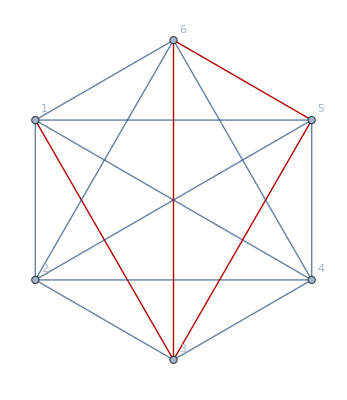

```mathematica
CompleteGraph[6,GraphHighlight->{1<->3,3<->5,3<->6,5<->6},GraphHighlightStyle->"Thick",VertexLabels->"Name"]
```

```mathematica
Table[With[
{g=GraphUnion[
GraphComplement[Graph[GraphFromSets[s1]]],
GraphComplement[Graph[GraphFromSets[s2]]]
]},
Labeled[
CompleteGraph[6,GraphHighlight->EdgeList[g],GraphHighlightStyle->"Thick"],
{EdgeList[g],Factor[ChromaticPolynomial[g,x]],PlanarGraphQ[g],ChromaticPolynomial[g,4]}
]
],{s1,quad1[6]},{s2,quad2[6]}]
```

```mathematica
Table[With[
{g=GraphUnion[
GraphComplement[Graph[GraphFromSets[s1]]],
GraphComplement[Graph[GraphFromSets[s2]]],
GraphComplement[Graph[GraphFromSets[s3]]],
GraphComplement[Graph[GraphFromSets[s4]]],
GraphComplement[Graph[GraphFromSets[s5]]]
]},
Labeled[
CompleteGraph[6,GraphHighlight->EdgeList[g],GraphHighlightStyle->"Thick"],
{EdgeList[g],Factor[ChromaticPolynomial[g,x]],PlanarGraphQ[g],ChromaticPolynomial[g,4]}
]
],{s1,quad1[6]},{s2,quad2[6]},{s3,quad3[6]},{s4,quad4[6]},{s5,quad5[6]}]//Flatten
```

```mathematica
MyGraph[g_]:=Labeled[
CompleteGraph[VertexCount[g],GraphHighlight->EdgeList[g],GraphHighlightStyle->"Thick",VertexLabels->"Name"],
{Factor[ChromaticPolynomial[g,x]],PlanarGraphQ[g],ChromaticPolynomial[g,4]}
]
```

```mathematica
ShowGraphsFor[nodes_]:=Map[{MyGraph[#[[1]]],#[[2]]}&,Tally[Flatten[Monitor[
Table[With[
{g=GraphUnion[
GraphComplement[Graph[GraphFromSets[s1]]],
GraphComplement[Graph[GraphFromSets[s2]]],
GraphComplement[Graph[GraphFromSets[s3]]],
GraphComplement[Graph[GraphFromSets[s4]]],
GraphComplement[Graph[GraphFromSets[s5]]]
]},
Graph[g, VertexLabels->"Name"]
],{s1,quad1[nodes]},{s2,quad2[nodes]},{s3,quad3[nodes]},{s4,quad4[nodes]},{s5,quad5[nodes]}],
{s1,s2,s3,s4,s5}
]],IsomorphicGraphQ]
]
```

```mathematica
Length[quad1[7]]^5
```

1048576

```mathematica
ShowGraphsFor[7]
```

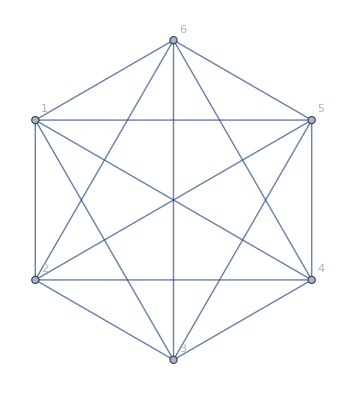
{{-Graphics-{(-2+x) (-1+x) x (-7+9 x-5 x^2+x^3),True,312},190},{-Graphics-{(-2+x) (-1+x) x (-11+13 x-6 x^2+x^3),True,216},505},{-Graphics-{(-2+x)^2 (-1+x) x (4-3 x+x^2),True,384},120},{-Graphics-{(-2+x)^2 (-1+x) x (2-2 x+x^2),True,480},20},{-Graphics-{(-3+x) (-2+x) (-1+x) x (5-4 x+x^2),True,120},179},{-Graphics-{(-2+x) (-1+x) x (-5+7 x-4 x^2+x^3),True,552},10}}

```mathematica
ShowGraphsFor[6]
```

```mathematica
ShowGraphsFor[7]
```